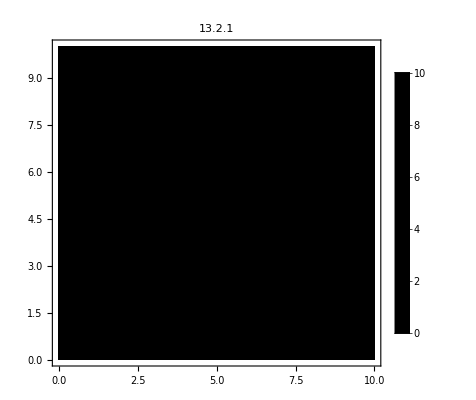

```mathematica
T1[x_,y_]=Re[20/π∑_(n=1)^∞ ((-1)^(n+1)/n Sin[(n π x)/10] ⅇ^(-(n π y)/10))];
DensityPlot[T1[x,y],{x,0,10},{y,0,10},PlotRange->All,PlotTheme->"Monochrome",PlotLegends->Automatic,PlotPoints->50,PlotLabel->Style["13.2.1",20]]
```

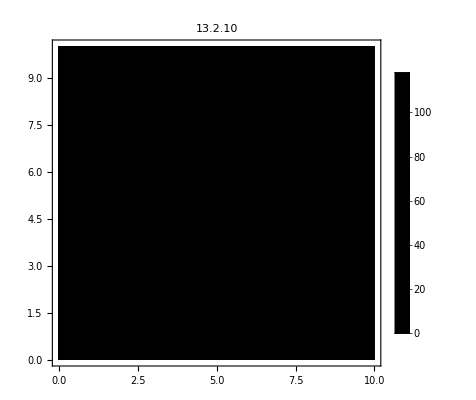

```mathematica
T2[x_,y_]=Re[∑_(n=1)^100 (-200/(n π Sinh[n π])((-1)^n-1)Sin[(n π x)/10]Sinh[(n π)/10(10-y)])];
DensityPlot[T2[x,y],{x,0,10},{y,0,10},PlotRange->All,PlotTheme->"Monochrome",PlotLegends->Automatic,PlotPoints->50,PlotLabel->Style["13.2.10",20]]
```

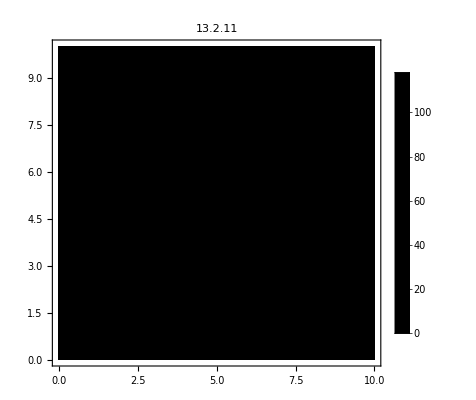

```mathematica
T3[x_,y_]=Re[∑_(n=1)^100 (-200/(n π Sinh[n π])((-1)^n-1)Sin[(n π x)/10]Sinh[(n π)/10(10-y)]-200/(n π Sinh[n π])((-1)^n-1)Sin[(n π y)/10]Sinh[(n π)/10(10-x)])];
DensityPlot[T3[x,y],{x,0,10},{y,0,10},PlotRange->All,PlotTheme->"Monochrome",PlotLegends->Automatic,PlotPoints->50,PlotLabel->Style["13.2.11",20]]
```

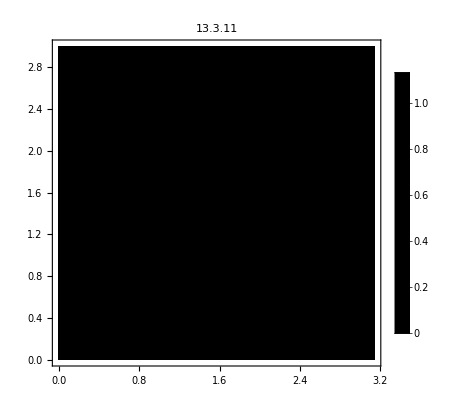

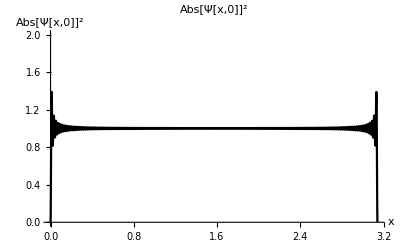

```mathematica
ψ[x_,t_]=∑_(n=1)^300 (-2/(n π)((-1)^n-1)Sin[n x] ⅇ^(-(ⅈ ℏ n^2)/(2m)t));
DensityPlot[Norm[ψ[x,t]]^2,{x,0,π},{t,0,3},PlotRange->All,PlotTheme->"Monochrome",PlotLegends->Automatic,PlotPoints->50,PlotLabel->Style["13.3.11",20]]
Plot[Norm[ψ[x,1]]^2,{x,0,π},PlotRange->{{0,π},{0,2}},PlotLabel->Style[Abs["Ψ[x,0]"]^2,20],AxesLabel->{x,Abs["Ψ[x,0]"]^2},PlotTheme->"Monochrome"]
```